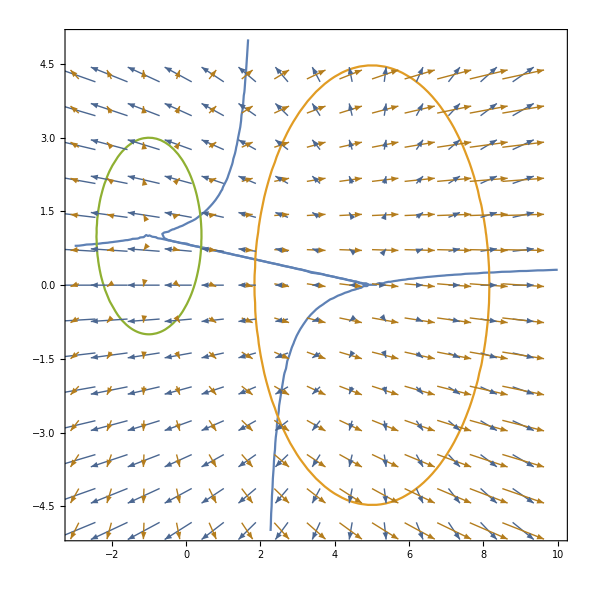

```mathematica
f[x_,y_]:=((x-5)^2)/2+((y)^2)/4
h[x_,y_]:=((x+1)^2)/2+((y-1)^2)/4
g[x_,y_] := Evaluate[Grad[f[x,y],{x,y}]]
r[x_,y_] := Evaluate[Grad[h[x,y],{x,y}]]
delta=

Show[
ContourPlot[{Normalize[g[x,y]]==-Normalize[r[x,y]],f[x,y]==5,h[x,y]==1},{x,-3,10},{y,-5,5}],
VectorPlot[{g[x,y],r[x,y]},{x,-3,10},{y,-5,5}]]
```

```mathematica
NSolve[Normalize[Grad[h[xa,ya],{xa,ya}]]==-Normalize[Grad[f[xb,yb],{xb,yb}]],{xa,ya,xb[xa],yb[yb]}]
```

{}

```mathematica
Evaluate[Grad[f[x,y],{x,y}]]
```

{x,y/2}

```mathematica
Grad[x^2/2+y^2/4,{x,y}]/.{y->1,x->10}
```

{10,1/2}

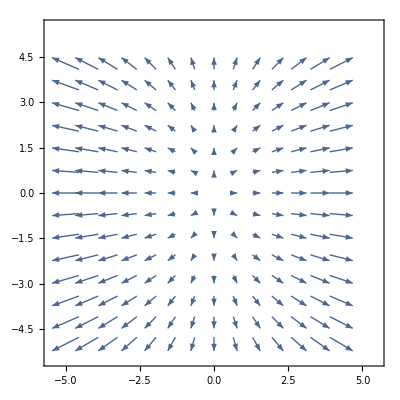

```mathematica
VectorPlot[Evaluate[Grad[f[x,y],{x,y}]],{x,-5,5},{y,-5,5}]
```

```mathematica
Rank[{1,0,0}]
```

Rank[{1,0,0}]

xb[xa] und yb[ya] sind die Punkte auf Ellipse B ausgedrückt in Abhängigkeit eines Punktes (xa,ya) auf Ellipse A:

```mathematica
Clear[xa]
```

```mathematica
Clear[ya]
```

```mathematica
xb[xa_]:=xa+(da1*(2*xa-2*aA1)*c)/(da1^2*(2*xa-2*aA1)^2+da2^2*(2*yA-2*aA2)^2)
```

```mathematica
yb[ya_]:=ya+(da2*(2*ya-2*aA2)*c)/(da1^2*(2*xA-2*aA1)^2+da2^2*(2*ya-2*aA2)^2)
```

Dies ist die vollständige Abstandsfunktion zwischen zwei beliebigen Punkten auf den Ellipsen.
Im folgenden wird die Abstandsfunktion durch einsetzten der obigen Herlietungen umgeformt und später der Gradient berechnet.

```mathematica
abs[xa_,ya_,xb_,yb_]=(xa-ya)^2+(xb-yb)^2
```

(xa-ya)^2+(xb-yb)^2

```mathematica
(xa-ya)^2+(xb-yb)^2
```

Gradient der Abstandsfunktion:

```mathematica
Grad[abs[xA,yA,xb[xA],yb[yA]],{xA,yA}]
```

{2 (xA-yA)+2 (1-(4 c da1^3 (-2 aA1+2 xA)^2)/((da1^2 (-2 aA1+2 xA)^2+da2^2 (-2 aA2+2 yA)^2)^2)+(4 c da1^2 da2 (-2 aA1+2 xA) (-2 aA2+2 yA))/((da1^2 (-2 aA1+2 xA)^2+da2^2 (-2 aA2+2 yA)^2)^2)+(2 c da1)/(da1^2 (-2 aA1+2 xA)^2+da2^2 (-2 aA2+2 yA)^2)) (xA-yA+(c da1 (-2 aA1+2 xA))/(da1^2 (-2 aA1+2 xA)^2+da2^2 (-2 aA2+2 yA)^2)-(c da2 (-2 aA2+2 yA))/(da1^2 (-2 aA1+2 xA)^2+da2^2 (-2 aA2+2 yA)^2)),-2 (xA-yA)+2 (-1-(4 c da1 da2^2 (-2 aA1+2 xA) (-2 aA2+2 yA))/((da1^2 (-2 aA1+2 xA)^2+da2^2 (-2 aA2+2 yA)^2)^2)+(4 c da2^3 (-2 aA2+2 yA)^2)/((da1^2 (-2 aA1+2 xA)^2+da2^2 (-2 aA2+2 yA)^2)^2)-(2 c da2)/(da1^2 (-2 aA1+2 xA)^2+da2^2 (-2 aA2+2 yA)^2)) (xA-yA+(c da1 (-2 aA1+2 xA))/(da1^2 (-2 aA1+2 xA)^2+da2^2 (-2 aA2+2 yA)^2)-(c da2 (-2 aA2+2 yA))/(da1^2 (-2 aA1+2 xA)^2+da2^2 (-2 aA2+2 yA)^2))}

Nebenbedingungen, wobei in Nebenbedingung zwei auch die Variablen wie oben ersetzt werden:

```mathematica
nebenA[xa_,ya_]=da1(xa-aA1)^2+da2(ya-aA2)^2-1
```

-1+da1 (-aA1+xa)^2+da2 (-aA2+ya)^2

```mathematica
nebenB[xb_,yb_]=db1(xb-aB1)^2+dB2(yb-aB2)^2-1
```

-1+db1 (-aB1+xb)^2+dB2 (-aB2+yb)^2

```mathematica
nebenBtoA[xA_,yB_]=nebenB[xb[xA],yb[yA]]
```

-1+db1 (-aB1+xA+(c da1 (-2 aA1+2 xA))/(da1^2 (-2 aA1+2 xA)^2+da2^2 (-2 aA2+2 yA)^2))^2+dB2 (-aB2+yA+(c da2 (-2 aA2+2 yA))/(da1^2 (-2 aA1+2 xA)^2+da2^2 (-2 aA2+2 yA)^2))^2

Gradient der Nebenbedingung A:

```mathematica
Grad[nebenA[xA,yA],{xA,yA}]
```

{2 da1 (-aA1+xA),2 da2 (-aA2+yA)}

auflösen der Gleichung nach (xA,yA)

```mathematica
Solve[Grad[abs[xA,yA,xb[xA],yb[yA]],{xA,yA}]==delta*Grad[nebenA[xA,yA],{xA,yA}]&&nebenA[xA,yA]==0&&nebenBtoA[xA,yA]==0,{xA,yA}]
```

$Aborted